```mathematica
x[t_]:=A*Exp[I*ω*t+I*ϕ];
```

```mathematica
x''[t]+γ*x'[t]+ω0^2*x[t]//FullSimplify
```

-A ⅇ^(ⅈ (ϕ+t ω)) (-ⅈ γ ω+ω^2-ω0^2)

```mathematica
FullSimplify[x''[t] + γ*x'[t]+ω0^2*x[t]-(F0/m)*Exp[I*ω*t]==0]
```

(ⅇ^(ⅈ t ω) (F0+A ⅇ^(ⅈ ϕ) m (-ⅈ γ ω+ω^2-ω0^2)))/m==0

```mathematica
Solve[(ⅇ^(ⅈ t ω) (F0+A ⅇ^(ⅈ ϕ) m (-ⅈ γ ω+ω^2-ω0^2)))/m==0,A]//FullSimplify
```

{{A→(ⅇ^(-ⅈ ϕ) F0)/(m (ⅈ γ ω-ω^2+ω0^2))}}

```mathematica
A=(F0/m)/Sqrt[(1-ρ^2)^2+(f*ρ)^2]/ω0^2;
```

```mathematica
D[(1-ρ^2)^2+(f*ρ)^2,ρ]//FullSimplify
```

2 ρ (-2+f^2+2 ρ^2)

```mathematica
Solve[D[(1-ρ^2)^2+(f*ρ)^2,ρ]==0,ρ]
```

{{ρ→0},{ρ→-(√(2-f^2))/(√2)},{ρ→(√(2-f^2))/(√2)}}

```mathematica
(F0/m)/Sqrt[(1-ρ^2)^2+(f*ρ)^2]/ω0^2/.{ρ->(√(2-f^2))/(√2)}//FullSimplify
```

(2 F0)/(√(-f^2 (-4+f^2)) m ω0^2)

```mathematica
2/(Sqrt[2]*Sqrt[4-Sqrt[2]^2])
```

1

```mathematica
-F0*a*ω^2/(2*Pi)*Integrate[Cos[ω*t]*Sin[ω*t+ϕ],{t,0,2*Pi/ω}]//FullSimplify
```

-1/2 a F0 ω Sin[ϕ]

```mathematica
-1/2 a F0 ω Sin[ϕ]/.{a->(F0/m)/Sqrt[(ω0^2-ω^2)^2+(γ*ω)^2],ϕ->-ArcTan[γ*ω/(ω0^2 - ω^2)]}//FullSimplify
```

(F0^2 γ ω^2)/(2 m (-ω^2+ω0^2) √(1+(γ^2 ω^2)/((ω^2-ω0^2)^2)) √(γ^2 ω^2+(ω^2-ω0^2)^2))

```mathematica
P=F0^2/(2*m*γ)*(γ*ω)^2/((ω0^2-ω^2)^2 + (γ*ω)^2);
```

```mathematica
Solve[D[P,ω]==0]
```

{{F0→0},{γ→0},{ω→0},{ω0→-ω},{ω0→-ⅈ ω},{ω0→ⅈ ω},{ω0→ω}}

```mathematica
-ω/(2*Pi)*m*γ*a^2*Integrate[(D[Cos[ω*t+ϕ],t])^2,{t,0,2*Pi/ω}]/.{a->(F0/m)/Sqrt[(ω0^2-ω^2)^2+(γ*ω)^2]}
```

-(F0^2 γ ω^2)/(2 m (γ^2 ω^2+(-ω^2+ω0^2)^2))

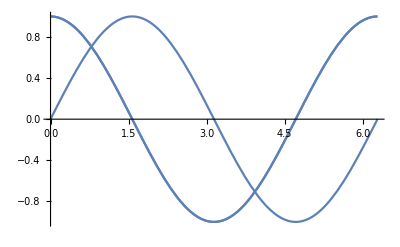

```mathematica
Show[Plot[Cos[t],{t,0,2*Pi}],Plot[Cos[t-Pi/2],{t,0,2*Pi}],Plot[-Sin[t-Pi/2],{t,0,2*Pi}]]
```

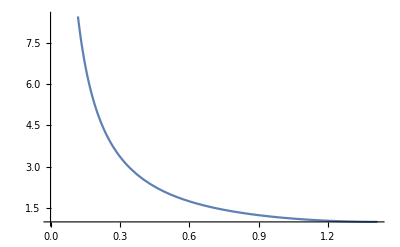

```mathematica
Plot[2/(f*Sqrt[4-f^2]),{f,0,Sqrt[2]}]
```

```mathematica
Manipulate[Plot[1/Sqrt[(1-ρ^2)^2+(f*ρ)^2],{ρ,0,2},PlotRange->{0,10}],{f,0,2}]
```

```mathematica
Solve[(1-(1-f^2/2))^2+f^2*(1-f^2/2)-1==0,f]
```

{{f→-√2},{f→-√2},{f→√2},{f→√2}}

```mathematica
(*resonant driving*)
```

```mathematica
DSolve[{y''[t]+γ*y'[t]+ω0^2*y[t]==F0/m*Cos[ω0*t]},y[t],t]//FullSimplify
```

{{y[t]→ⅇ^(-1/2 t (γ+√(γ^2-4 ω0^2))) (C[1]+ⅇ^(t √(γ^2-4 ω0^2)) C[2])+(F0 Sin[t ω0])/(m γ ω0)}}

```mathematica
(*resonant driving steady state solution*)
```

```mathematica
z[t_]:=(F0 Sin[t ω0])/(m γ ω0);
```

```mathematica
Integrate[Sin[t ω0]^2,{t,0,2*Pi/ω0}]
```

π/ω0

```mathematica
(*Total energy from the drive*)
```

```mathematica
KE=(ω0/(2*Pi))Integrate[(1/2)*m*z'[t]^2,{t,0,2*Pi/ω0}];
```

```mathematica
PE=(ω0/(2*Pi))Integrate[(1/2)*m*ω0^2*z[t]^2,{t,0,2*Pi/ω0}];
```

```mathematica
KE
```

F0^2/(4 m γ^2)

```mathematica
EStored=KE+PE
```

F0^2/(2 m γ^2)

```mathematica
(*E lost = work done by drag = \integral \gamma * m * v[t] * v[t] = *)
```

```mathematica
ELost=Integrate[γ*z'[t]^2*m,{t,0,2*Pi/ω0}]
```

(F0^2 π)/(m γ ω0)

```mathematica
Q =2*Pi* EStored/ELost
```

ω0/γ

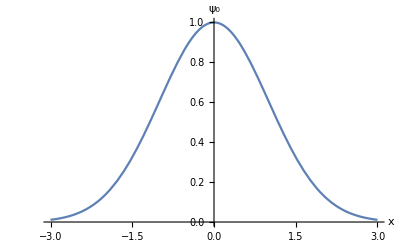

```mathematica
A0=Plot[E^(-x^2/2),{x,-3,3},Ticks->None,AxesLabel->{x,Subscript[ψ, 0]}]
```

```mathematica
D[E^(-x^2/2),x]
```

-ⅇ^(-x^2/2) x

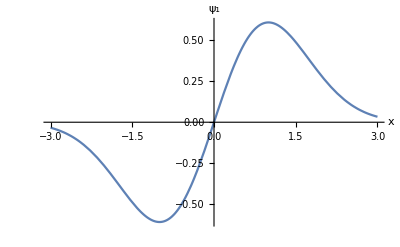

```mathematica
A1=Plot[ⅇ^(-x^2/2) x,{x,-3,3},Ticks->None,AxesLabel->{x,Subscript[ψ, 1]}]
```